```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
y = 0.0001/(x(x-1))
```

0.0001/((-1+x) x)

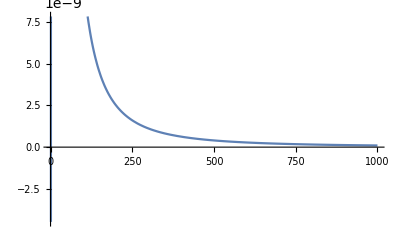

```mathematica
Plot[y,{x,0,1000}]
```

```mathematica
chidata =Import["chi.txt", "CSV"]
```

{{1,197},{2,367},{3,464},{4,862},{5,1255},{6,1371},{7,1274},{8,1176},{9,1037},{10,858},{11,402},{12,236},{13,195},{14,113},{15,37},{16,4},{17,3},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},9695,{9774,0},{9775,0},{9776,0},{9777,0},{9778,0},{9779,0},{9780,0},{9781,0},{9782,0},{9783,0},{9784,0},{9785,0},{9786,0},{9787,0},{9788,0},{9789,0},{9790,0},{9791,0},{9792,0},{9793,0},{9794,0},{9795,0},{9796,0},{9797,0},{9798,0},{9799,0},{9800,0},{9801,0},{9802,0},{9803,0},{9804,0},{9805,0},{9806,0},{9807,0},{9808,0},{9809,0},{9810,0},{9811,0},{9812,0},{9813,0},{9814,0},{9815,0},{9816,0},{9817,0},{9818,0},{9819,0},{9820,0},{9821,0},{9822,0},{9823,0},{9824,0},{9825,0},{9826,0},{9827,0},{9828,0},{9829,0},{9830,0},{9831,0},{9832,0},{9833,0},{9834,0},{9835,0},{9836,0},{9837,0},{9838,0},{9839,0},{9840,0},{9841,0},{9842,0},{9843,0},{9844,0},{9845,0},{9846,0},{9847,0},{9848,0},{9849,0},{9850,0}}
 |  |  |  |

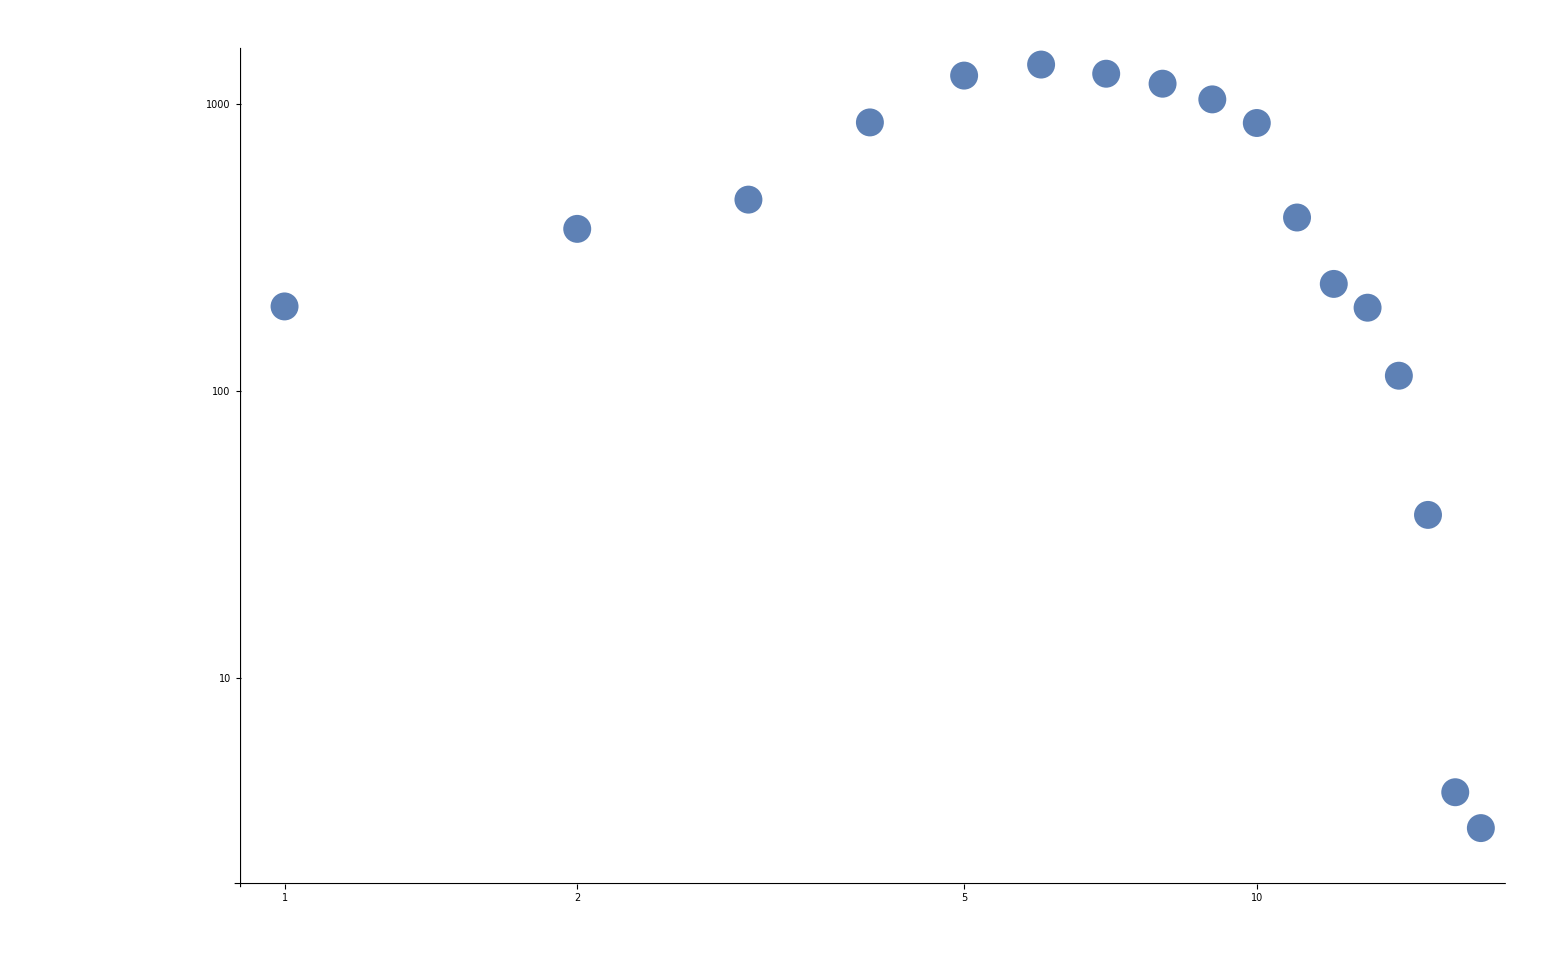

```mathematica
ListLogLogPlot[{chidata},PlotRange->All]
```

```mathematica
datanew=Import["array.txt", "CSV"]
```

{1}
 |  |  |  |

```mathematica
ArrayPlot[datanew, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
chinewdata = Import["chinew.txt", "CSV"]
```

{{0,1},{1,3158},{2,1314},{3,652},{4,454},{5,339},{6,273},{7,217},{8,171},{9,144},{10,124},{11,95},{12,115},{13,89},{14,66},{15,77},{16,71},{17,50},{18,56},{19,52},{20,47},{21,45},{22,45},{23,37},{24,24},{25,22},{26,38},{27,33},{28,33},{29,29},{30,19},{31,21},{32,25},{33,24},{34,21},{35,16},{36,16},{37,22},{38,19},{39,22},{40,27},{41,15},{42,16},{43,13},{44,11},{45,13},{46,17},{47,16},{48,16},{49,10},{50,7},{51,16},{52,14},{53,12},{54,16},{55,17},{56,8},{57,9},{58,13},{59,9},{60,9},{61,11},{62,5},{63,9},{64,11},{65,13},{66,9},{67,12},{68,15},{69,16},{70,11},{71,5},{72,5},{73,5},{74,9},9702,{9777,0},{9778,0},{9779,0},{9780,0},{9781,0},{9782,0},{9783,0},{9784,0},{9785,0},{9786,0},{9787,0},{9788,0},{9789,0},{9790,0},{9791,0},{9792,0},{9793,0},{9794,0},{9795,0},{9796,0},{9797,0},{9798,0},{9799,0},{9800,0},{9801,0},{9802,0},{9803,0},{9804,0},{9805,0},{9806,0},{9807,0},{9808,0},{9809,0},{9810,0},{9811,0},{9812,0},{9813,0},{9814,0},{9815,0},{9816,0},{9817,0},{9818,0},{9819,0},{9820,0},{9821,0},{9822,0},{9823,0},{9824,0},{9825,0},{9826,0},{9827,0},{9828,0},{9829,0},{9830,0},{9831,0},{9832,0},{9833,0},{9834,0},{9835,0},{9836,0},{9837,0},{9838,0},{9839,0},{9840,0},{9841,0},{9842,0},{9843,0},{9844,0},{9845,0},{9846,1},{9847,0},{9848,0},{9849,0},{9850,0},{9851,0}}
 |  |  |  |

```mathematica
dataacc=chinewdata;
dataacc[[All,2]]=9729-Accumulate[(chinewdata[[All,2]])]
```

{9728,6570,5256,4604,4150,3811,3538,3321,3150,3006,2882,2787,2672,2583,2517,2440,2369,2319,2263,2211,2164,2119,2074,2037,2013,1991,1953,1920,1887,1858,1839,1818,1793,1769,1748,1732,1716,1694,1675,1653,1626,1611,1595,1582,1571,1558,1541,1525,1509,1499,1492,1476,1462,1450,1434,1417,1409,1400,1387,1378,1369,1358,1353,1344,1333,1320,1311,1299,1284,1268,1257,1252,1247,1242,1233,1226,1222,1212,1205,1196,1187,1179,1173,1165,1154,1147,1144,1137,1129,1119,1109,1105,1099,1093,1086,1080,1075,1067,1062,1060,1052,1047,1044,1039,1029,1023,1020,1010,1007,1000,996,989,984,984,982,977,976,971,964,962,958,955,950,946,943,939,931,926,925,921,917,913,911,908,906,900,898,897,893,888,886,884,881,880,873,870,864,858,856,853,850,847,845,845,843,842,839,834,830,826,824,821,819,815,813,810,808,807,805,800,797,795,794,790,788,788,786,785,784,781,779,778,776,774,774,772,771,771,766,763,762,756,756,752,750,748,746,744,742,741,740,736,734,731,728,726,724,722,722,719,718,717,717,717,714,711,709,708,706,705,702,700,696,695,695,694,693,690,686,686,684,679,677,676,675,672,671,668,668,668,668,668,665,664,660,658,657,656,655,653,650,647,647,645,645,644,642,640,640,640,638,638,636,634,633,633,632,630,630,627,626,626,624,624,621,619,618,618,616,615,614,613,612,611,610,609,608,607,606,606,606,604,604,601,600,597,596,595,594,593,593,592,592,591,589,587,587,587,585,585,585,585,585,584,583,582,580,578,578,578,576,575,574,574,573,572,571,567,567,565,563,562,561,560,560,559,557,557,557,556,556,554,553,553,551,551,549,549,548,545,545,545,543,543,543,542,540,539,538,537,537,535,534,534,532,531,531,531,531,530,530,528,528,527,526,524,524,524,524,524,523,523,523,523,523,523,521,520,520,520,520,518,517,516,516,516,516,516,515,514,514,514,513,512,511,511,509,508,507,507,505,504,504,503,503,502,501,501,501,501,500,499,499,499,497,497,497,497,495,495,494,494,493,490,488,488,487,487,487,487,484,483,483,482,482,480,478,478,476,474,473,471,470,470,470,470,469,468,468,468,467,463,460,457,454,454,454,454,453,453,452,452,452,452,450,448,448,448,448,448,446,445,445,445,445,444,444,444,442,441,441,441,441,440,439,439,439,438,438,438,437,436,435,435,434,434,434,433,432,432,431,431,431,431,431,431,431,431,430,429,429,429,427,427,427,427,427,426,426,425,425,424,424,424,423,422,422,421,421,420,420,420,419,419,419,419,419,419,418,418,417,416,416,416,416,415,415,414,414,413,413,412,412,412,411,411,410,410,410,410,409,409,409,407,406,406,405,405,405,405,405,405,405,405,404,403,403,403,403,402,402,402,402,402,401,401,401,401,401,401,401,400,400,400,398,398,398,397,397,397,397,397,395,395,394,394,394,394,392,392,392,392,392,392,392,392,392,392,390,389,389,389,389,389,388,387,387,385,385,385,385,385,385,383,382,382,382,382,382,382,382,382,381,381,381,381,381,381,381,381,380,379,378,378,378,377,375,375,375,375,375,375,375,375,375,375,375,373,372,371,371,371,370,370,370,370,369,369,369,369,369,369,369,368,367,367,367,367,366,365,364,363,362,362,362,362,361,361,361,360,360,360,360,360,359,357,357,357,356,356,356,356,355,354,354,354,354,354,354,354,354,354,354,354,354,354,354,353,353,353,353,353,353,353,353,353,352,352,352,352,352,352,352,352,352,352,352,352,352,351,351,351,351,350,349,349,349,349,347,346,345,345,344,343,343,343,343,343,342,342,342,340,339,339,338,338,338,337,337,337,337,337,337,337,337,336,335,335,335,335,335,335,335,335,335,334,334,334,333,333,332,331,329,329,329,329,329,329,329,329,329,329,329,329,328,328,328,328,328,328,328,328,328,328,328,328,327,327,327,327,326,326,326,325,325,325,325,324,324,323,323,321,321,320,320,320,320,319,319,319,319,319,319,319,319,319,318,318,318,318,317,316,316,316,316,316,316,316,316,316,316,316,316,316,316,316,316,315,315,315,315,315,315,314,314,314,314,314,314,314,314,314,314,314,314,314,313,313,313,312,311,311,311,310,310,309,308,308,308,308,307,307,307,307,307,307,307,307,307,307,307,307,307,307,307,307,307,306,306,306,305,305,305,305,305,305,305,305,305,304,304,304,303,303,303,303,303,303,303,302,302,301,301,301,301,301,301,301,301,301,301,300,300,299,299,298,298,297,297,297,296,296,296,296,296,296,296,296,296,295,295,295,295,295,294,294,293,293,293,293,293,293,293,293,292,292,292,292,291,291,289,289,289,289,288,287,287,287,287,286,285,285,285,285,285,285,285,285,284,283,283,282,282,281,281,281,280,280,280,280,280,279,279,279,279,279,279,279,279,279,279,277,277,276,275,275,275,275,275,274,273,272,272,272,272,272,272,271,271,271,270,270,270,270,270,269,269,269,269,269,269,269,269,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,267,267,267,266,266,266,266,266,265,265,265,265,265,265,265,265,265,264,263,263,263,263,263,263,263,263,263,263,263,263,263,261,261,260,260,260,259,259,259,259,259,258,257,257,257,255,255,255,255,255,254,254,254,254,254,254,254,254,254,254,254,253,252,252,251,251,250,250,249,249,249,249,249,249,249,249,249,249,248,248,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,244,244,244,244,244,244,244,244,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,240,240,240,240,240,240,240,239,238,238,238,238,238,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,236,235,235,235,234,234,234,234,234,234,234,234,234,234,234,234,234,234,234,234,233,233,233,233,233,233,233,233,233,233,232,232,232,232,232,232,232,232,232,232,232,232,232,232,232,232,232,231,230,230,230,230,230,230,230,230,229,229,229,229,229,229,229,229,229,229,229,229,229,229,229,229,229,228,228,228,228,228,228,228,228,228,227,227,227,227,227,227,227,227,227,227,227,226,226,226,226,226,226,225,225,225,225,224,224,224,224,224,224,224,224,224,224,224,223,223,223,223,223,222,222,222,222,222,222,222,222,222,222,222,222,222,221,221,221,221,221,221,221,221,221,221,221,220,220,220,220,220,220,220,220,220,220,220,219,219,219,219,219,219,218,218,218,218,218,218,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,215,215,215,215,215,215,215,215,215,215,215,215,215,215,215,215,215,215,214,214,214,214,213,213,213,212,212,212,212,212,212,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,210,210,210,210,210,210,210,210,210,210,210,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,206,205,205,205,205,205,204,204,204,204,204,204,204,204,203,202,202,202,202,202,201,201,201,201,201,201,201,201,200,200,200,199,199,199,199,199,199,198,198,198,198,198,198,198,198,198,198,198,198,198,198,198,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,195,195,195,195,195,195,195,195,194,194,194,194,194,194,194,194,194,194,194,194,194,194,194,194,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,192,191,191,191,191,191,191,191,191,191,191,191,191,191,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,189,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,187,187,187,187,187,186,186,186,186,186,186,186,185,185,185,185,185,185,185,185,185,185,185,185,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,183,182,182,182,182,182,182,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,179,179,179,179,179,179,178,178,178,178,178,178,178,178,178,178,178,178,178,178,177,177,177,176,175,175,175,175,175,175,175,175,175,175,175,175,174,174,174,174,174,174,174,174,174,174,174,173,173,173,173,173,173,173,173,173,173,172,172,172,172,172,172,172,172,172,172,172,172,172,172,172,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,170,170,170,170,169,168,168,168,168,168,168,168,168,168,168,168,168,168,167,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,165,165,165,165,165,165,165,164,164,164,164,164,164,164,164,164,164,164,163,163,163,163,163,163,163,163,163,163,163,163,163,162,162,162,162,162,162,162,162,162,162,162,162,162,161,161,161,161,161,161,161,161,161,161,160,159,159,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,156,156,156,156,156,156,156,156,156,156,156,156,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,154,154,154,154,154,154,154,154,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,152,152,152,152,151,151,151,151,151,151,151,151,151,151,151,151,151,151,151,151,151,151,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,149,149,149,149,149,148,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,145,145,145,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,141,141,141,141,141,141,141,141,141,141,141,141,141,141,140,140,140,140,140,140,140,140,139,139,139,139,139,139,139,139,139,139,139,139,139,139,139,139,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,137,136,136,136,136,136,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,134,134,134,134,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,130,130,130,130,130,130,130,130,130,130,129,129,129,129,129,129,129,129,129,129,129,129,129,129,128,128,128,128,128,128,128,128,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,124,124,124,124,124,124,124,124,124,123,123,123,123,123,123,123,123,123,123,123,123,123,123,123,123,122,122,122,122,122,122,122,122,122,122,122,122,122,122,122,122,122,122,121,121,121,121,121,121,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,119,119,119,119,119,119,119,119,119,119,119,119,119,119,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,117,117,117,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,114,114,114,114,114,114,114,114,114,114,114,114,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,112,112,112,112,112,112,112,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,110,110,109,109,109,109,108,108,108,107,107,107,107,107,107,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,105,105,105,105,105,105,105,104,104,104,104,104,104,104,104,104,104,104,104,104,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,100,100,100,100,100,100,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,97,97,97,97,97,97,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,88,87,87,87,87,87,87,87,87,87,87,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,82,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,80,80,80,80,79,79,79,79,79,79,79,79,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,70,70,70,70,70,70,70,70,70,69,69,69,69,69,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,65,65,65,65,65,65,65,65,65,65,65,65,65,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0}

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

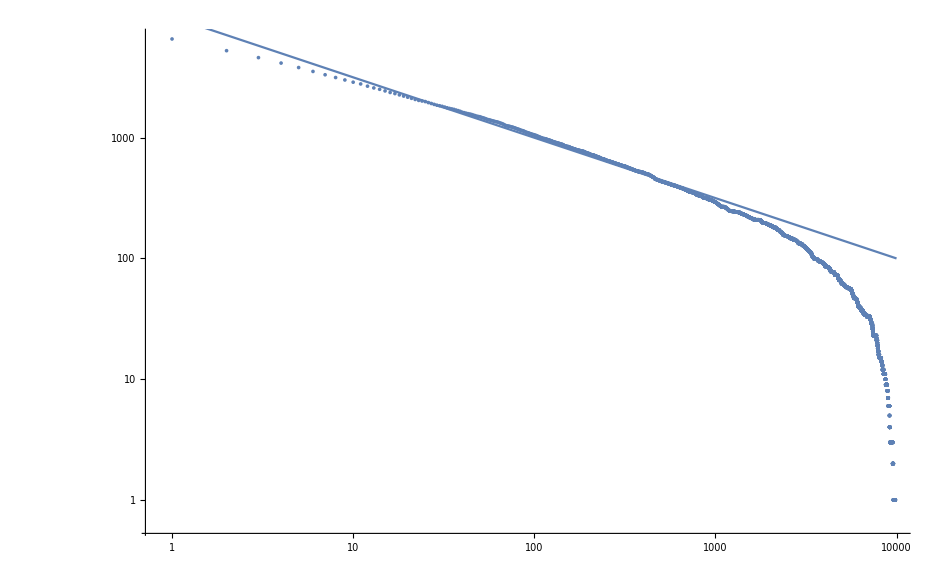

```mathematica
Show[ListLogLogPlot[{dataacc},PlotRange->All],LogLogPlot[10000/(x^0.5),{x,0.5,10000}]]
```

```mathematica
f = Import["fplot.txt" , "CSV"]
```

{{0,0},{1.17775×10^-6,7},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.0095×10^-6,6},{0.0231816,137781},{5.72049×10^-6,34},{1.6825×10^-7,1},{0.0148819,88451},{0.000342388,2035},{0.00897663,53353},{1.6825×10^-7,1},{5.04749×10^-7,3},{6.72999×10^-7,4},{0.0274045,162880},{1.6825×10^-7,1},{0.000014133,84},{0.00849324,50480},{3.70149×10^-6,22},{5.04749×10^-7,3},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.0095×10^-6,6},{0.0181451,107846},{1.6825×10^-7,1},{0.0000124505,74},{0.0000370149,220},{1.6825×10^-7,1},{5.04749×10^-7,3},{1.6825×10^-7,1},{6.72999×10^-7,4},{0.0000307897,183},{0.0000139647,83},{2.019×10^-6,12},{1.6825×10^-7,1},9777,{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{5.04749×10^-7,3},{5.04749×10^-7,3},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1}}
 |  |  |  |

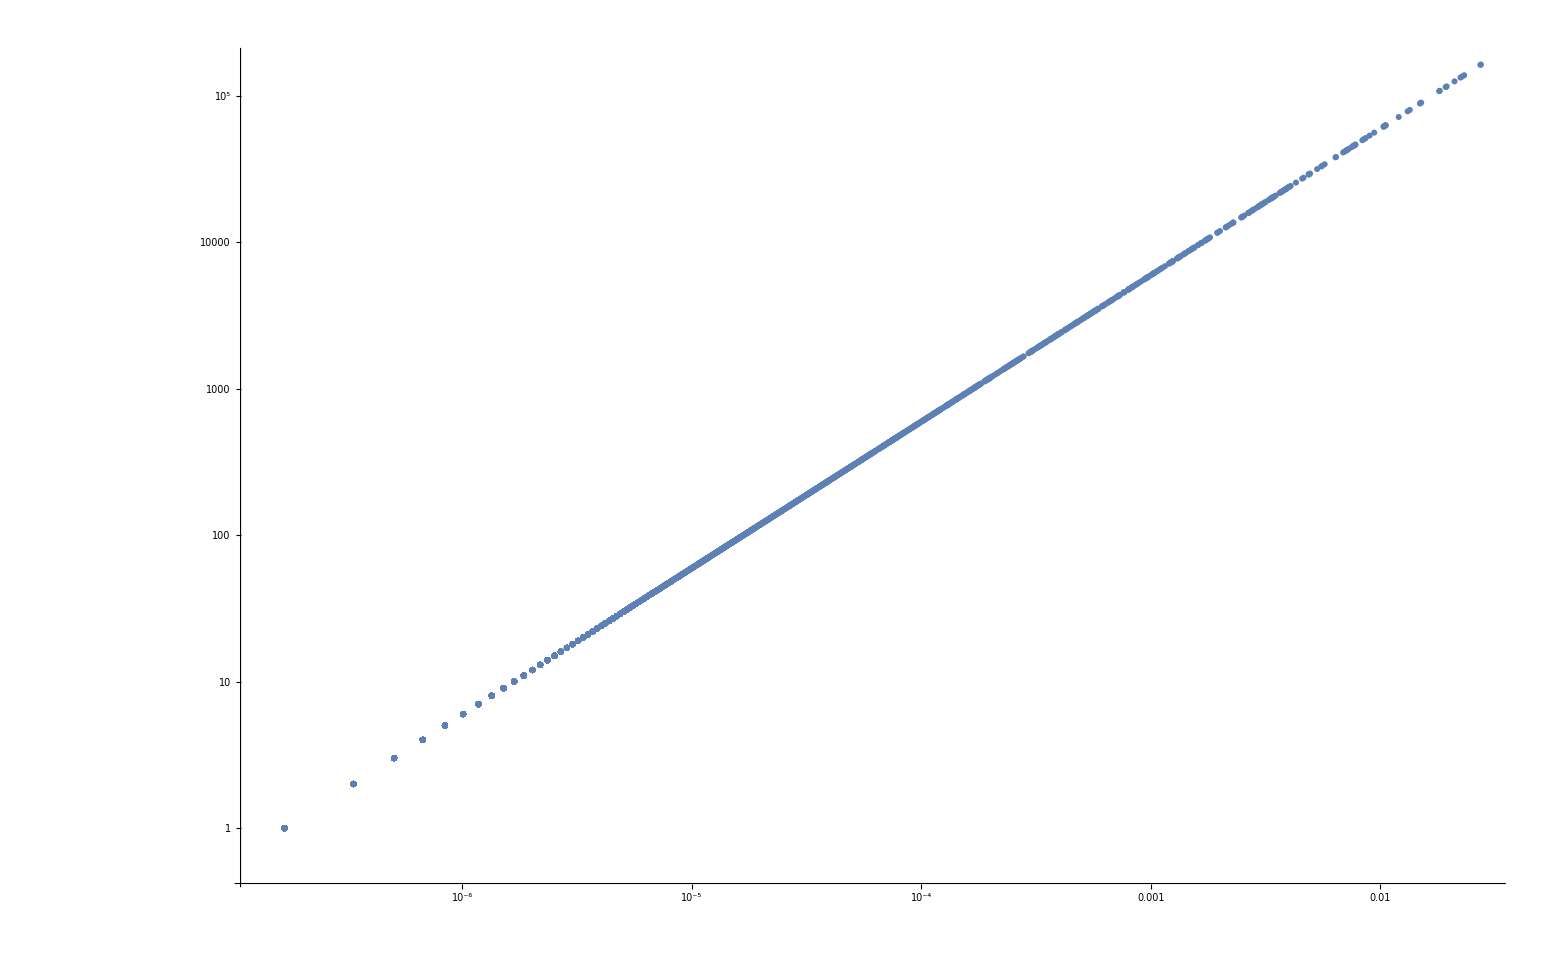

```mathematica
ListLogLogPlot[f]
```